# Experiment 12 - Electron Diffraction

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Linear Relation

We observe from the pre-lab that λ=hc/(√(2 mc^2 eV)) and under a small-angle approximation r/x=(K̂)/(2π)λ/a_0. This gives r=((K̂)/(2π)hcx/(a_0 √(2 mc^2 e)))v^(-1/2) the linear relation between r and V^(-1/2).

 We first calculate K̂ for the features we are concerned with:
 
 	For graphite: (K̂)_1=(4π)/(√3); (K̂)_2=4π ; (K̂)_3=(8π)/(√3)
 	For aluminium: (K̂)_1=2π √3; (K̂)_2= 4π ; (K̂)_3=4π √2; (K̂)_4=8π

```mathematica
(* We set some constants to help with the analysis later *)
graphitek1=(4 π)/(√3);
graphitek2=4 π;
graphitek3=(8 π)/(√3);
aluminiumk1=2 π √3;
aluminiumk2=4 π;
aluminiumk3=4 π √2;
aluminiumk4=8 π;
graphitea0=0.24612*10^-9 (*m*);
aluminiuma0=4.050*10^-10 (*m*);
x=0.178 (*m*);
c=2.998*10^8 (*ms^-1*);
mc2=0.511*10^6 (*J*);
```

This allows us to define the following function to calculate h with uncertainty from our fit data.

```mathematica
h[slope_,error_,featureK_,featurea0_]:={ScientificForm[(slope*2π*featurea0*Sqrt[2*mc2])/(featureK*x*c),3],ScientificForm[(error*2π*featurea0*Sqrt[2*mc2])/(featureK*x*c),2]}
```

## Data Analysis

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

Graphite

## First (closest to direct beam) diffraction feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/graphite1.dat

File comment header:

V (kV) d1 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 15 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 15 points transformed.

```mathematica
LinearFit[]
```

n = 15

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.00146151 | b= 
0.961029 | 
σ_a= 
0.00048536 | σ_b= 
0.0397627 | Std. deviation= 
0.000196185

Fit of (x,y±σ_y)

a= 
0.00151375 | b= 
0.955306 | 
σ_a= 
0.000478305 | σ_b= 
0.0409109 | χ^2/(n-2)= 
1.07379

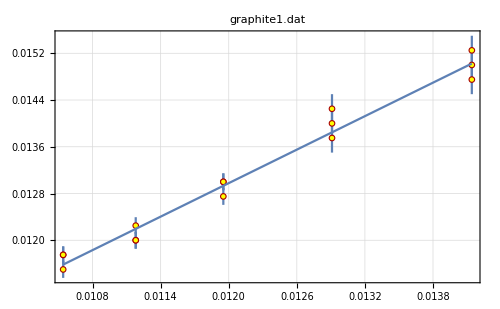
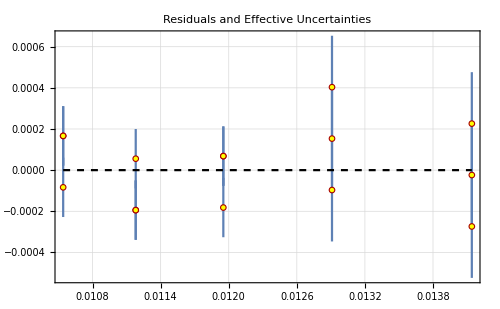
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.00151375 | b= 
0.955306 | 
σ_a= 
0.000478305 | σ_b= 
0.0409109 | χ^2/(n-2)= 
1.07379

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
hg1=h[0.955306,0.0409109,graphitek1,graphitea0]
```

{3.86×10^-15,1.7×10^-16}

## Second Diffraction Feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/graphite2.dat

File comment header:

V (kV) d2 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 15 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 15 points transformed.

```mathematica
LinearFit[]
```

n = 15

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00526492 | b= 
2.54134 | 
σ_a= 
0.00281902 | σ_b= 
0.230949 | Std. deviation= 
0.00113951

Fit of (x,y±σ_y)

a= 
-0.00676163 | b= 
2.63722 | 
σ_a= 
0.000383471 | σ_b= 
0.0312764 | χ^2/(n-2)= 
41.566

```mathematica
(* We observe an abnormally high (χ̃)^2 and an outlier at the V = 9 kV data point. We remove this data point and attempt another fit. *)
```

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{0.0104659,0.0106175}

n= 12

3 points removed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.00338906 | b= 
1.88358 | 
σ_a= 
0.000930216 | σ_b= 
0.0738571 | Std. deviation= 
0.000283473

Fit of (x,y±σ_y)

a= 
0.00317585 | b= 
1.89349 | 
σ_a= 
0.000580255 | σ_b= 
0.0451687 | χ^2/(n-2)= 
1.90987

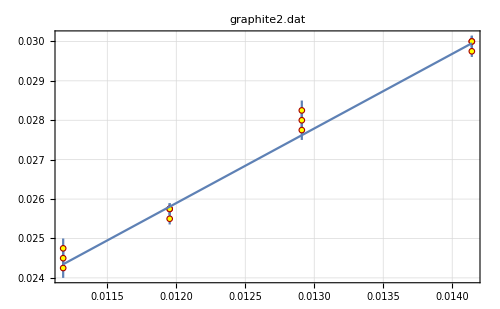
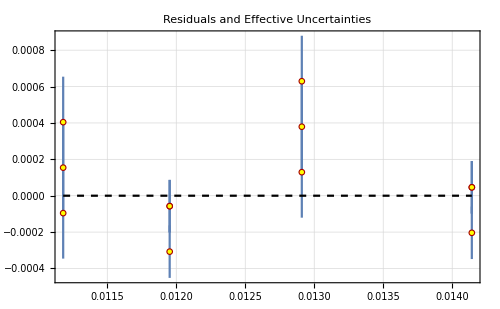
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.00317585 | b= 
1.89349 | 
σ_a= 
0.000580255 | σ_b= 
0.0451687 | χ^2/(n-2)= 
1.90987

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
hg2=h[1.839349,0.0451687,graphitek2,graphitea0]
```

{4.29×10^-15,1.1×10^-16}

## Third Diffraction Feature

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/graphite3.dat

File comment header:

V (kV) d3 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 15 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 15 points transformed.

```mathematica
LinearFit[]
```

n = 15

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.00188829 | b= 
3.10921 | 
σ_a= 
0.00108943 | σ_b= 
0.0892117 | Std. deviation= 
0.000440162

Fit of (x,y±σ_y)

a= 
0.000109292 | b= 
3.24072 | 
σ_a= 
0.000461991 | σ_b= 
0.0367481 | χ^2/(n-2)= 
2.75972

```mathematica
(* We observe slight anomalous behavior (within error margin) at the V = 9.0 kV data point. We remove this point to see if we obtain a better fit. *)
```

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{0.0104659,0.0106645}

n= 12

3 points removed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00082914 | b= 
3.31575 | 
σ_a= 
0.000833974 | σ_b= 
0.0662238 | Std. deviation= 
0.000254145

Fit of (x,y±σ_y)

a= 
-0.000668698 | b= 
3.29863 | 
σ_a= 
0.000494201 | σ_b= 
0.0390012 | χ^2/(n-2)= 
1.42234

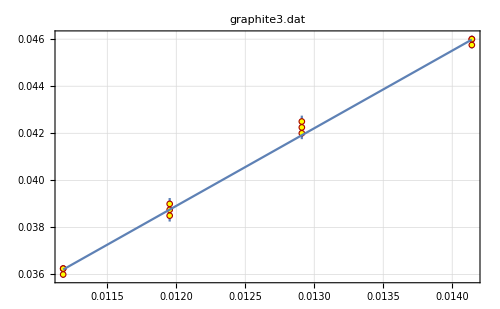
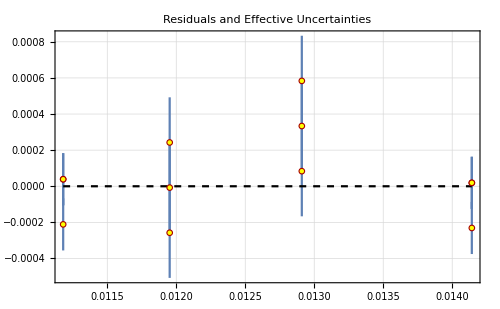
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.000668698 | b= 
3.29863 | 
σ_a= 
0.000494201 | σ_b= 
0.0390012 | χ^2/(n-2)= 
1.42234

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
hg3=h[3.29863,0.0390012,graphitek3,graphitea0]
```

{6.66×10^-15,7.9×10^-17}

Aluminium

## First Diffraction Feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/aluminium1.dat

File comment header:

V (kV) d1 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 12 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 12 points transformed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.000373444 | b= 
0.990918 | 
σ_a= 
0.00068478 | σ_b= 
0.0586499 | Std. deviation= 
0.000179785

Fit of (x,y±σ_y)

a= 
-9.4456×10^-6 | b= 
0.961454 | 
σ_a= 
0.000675513 | σ_b= 
0.0567942 | χ^2/(n-2)= 
1.06526

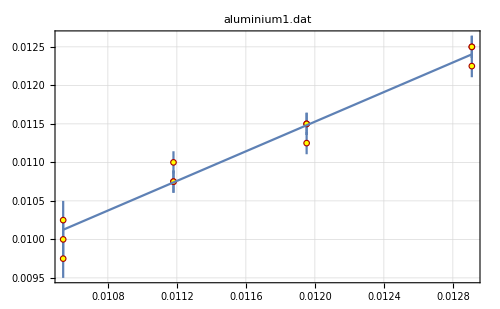
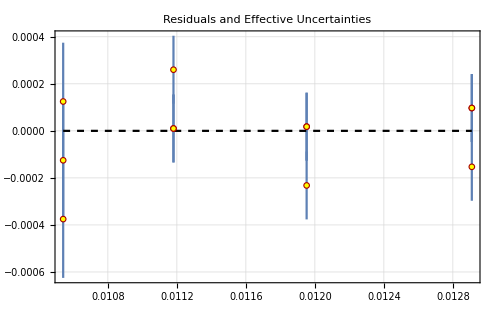
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-9.4456×10^-6 | b= 
0.961454 | 
σ_a= 
0.000675513 | σ_b= 
0.0567942 | χ^2/(n-2)= 
1.06526

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
ha1=h[0.961454,0.0567942,aluminiumk1,aluminiuma0]
```

{4.26×10^-15,2.5×10^-16}

## Second Diffraction Feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/aluminium2.dat

File comment header:

V (kV) d2 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 12 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 12 points transformed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00220291 | b= 
1.3269 | 
σ_a= 
0.000708172 | σ_b= 
0.0606243 | Std. deviation= 
0.000185891

Fit of (x,y±σ_y)

a= 
-0.00220291 | b= 
1.3269 | 
σ_a= 
0.000549919 | σ_b= 
0.0470845 | χ^2/(n-2)= 
1.65867

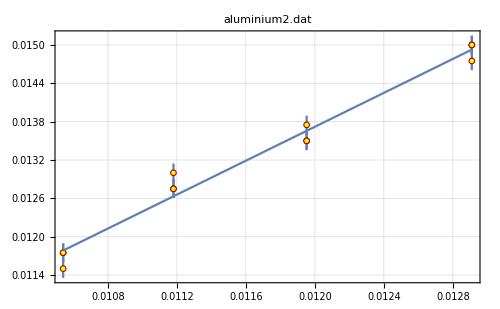
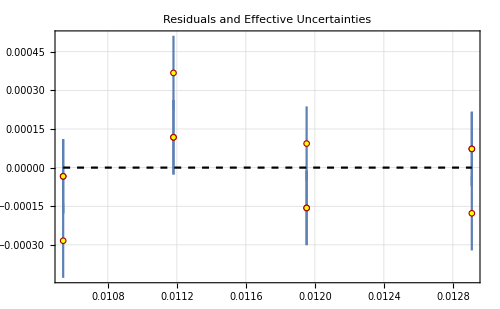
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.00220291 | b= 
1.3269 | 
σ_a= 
0.000549919 | σ_b= 
0.0470845 | χ^2/(n-2)= 
1.65867

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
ha2=h[1.3269,0.0470845,aluminiumk2,aluminiuma0]
```

{5.09×10^-15,1.8×10^-16}

## Third Diffraction Feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/aluminium3.dat

File comment header:

V (kV) d3 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 12 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 12 points transformed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00214772 | b= 
1.74613 | 
σ_a= 
0.000621888 | σ_b= 
0.0532458 | Std. deviation= 
0.00016319

Fit of (x,y±σ_y)

a= 
-0.00210654 | b= 
1.7428 | 
σ_a= 
0.000675506 | σ_b= 
0.0567936 | χ^2/(n-2)= 
0.877183

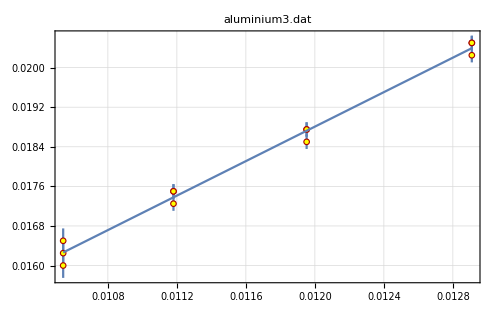
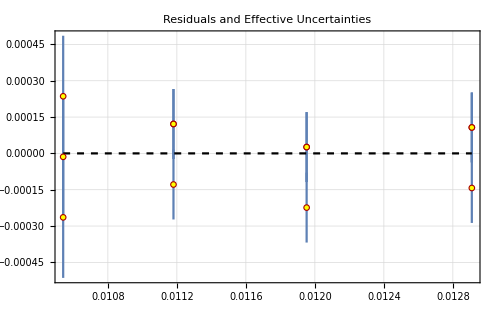
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.00210654 | b= 
1.7428 | 
σ_a= 
0.000675506 | σ_b= 
0.0567936 | χ^2/(n-2)= 
0.877183

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* Calculating h *)
ha3=h[1.7428,0.0567936,aluminiumk3,aluminiuma0]
```

{4.73×10^-15,1.5×10^-16}

## Fourth Diffraction Feature

```mathematica
(* Import and prepare the data for analysis *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/aluminium4.dat

File comment header:

V (kV) d4 (cm)

LoadFile::sorted: Data sorted in increasing x order.

Read 12 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2*0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 12 points transformed.

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.000244407 | b= 
1.81801 | 
σ_a= 
0.00105171 | σ_b= 
0.0900916 | Std. deviation= 
0.00027611

Fit of (x,y±σ_y)

a= 
0.000362479 | b= 
1.80915 | 
σ_a= 
0.000570581 | σ_b= 
0.0484501 | χ^2/(n-2)= 
3.19905

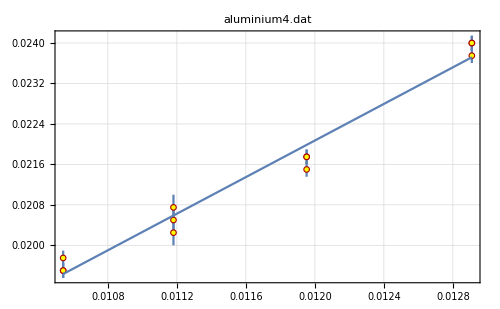
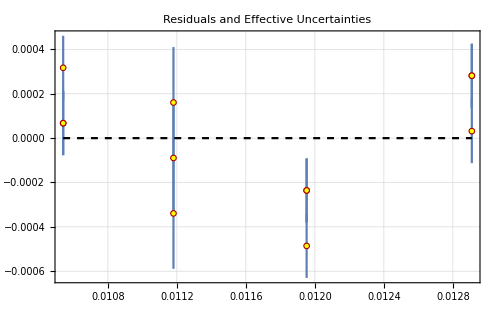
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.000362479 | b= 
1.80915 | 
σ_a= 
0.000570581 | σ_b= 
0.0484501 | χ^2/(n-2)= 
3.19905

```mathematica
LinearDifferencePlot[]
```

No obviously anomalous point is found, but the high error involved in measuring the very dim fourth diffraction feature and high (χ̃)^2 indicate that we should discount this feature when calculating h.

All data

We attempt to fit the entire data set by first scaling data from each diffraction feature by its (k̂)/(2π a_0).

```mathematica
graphite1data=Import["graphite1.dat"];
graphite1=Table[{graphite1data[[i]][[1]],(0.01*graphite1data[[i]][[2]]*2 π graphitea0)/graphitek1},{i,3,Length[graphite1data]}];
graphite2data=Import["graphite2.dat"];
graphite2=Table[{graphite2data[[i]][[1]],(0.01*graphite2data[[i]][[2]]*2 π graphitea0)/graphitek2},{i,4,Length[graphite2data]}];
graphite3data=Import["graphite3.dat"];
graphite3=Table[{graphite3data[[i]][[1]],(0.01*graphite3data[[i]][[2]]*2 π graphitea0)/graphitek3},{i,4,Length[graphite3data]}];
aluminium1data=Import["aluminium1.dat"];
aluminium1=Table[{aluminium1data[[i]][[1]],(0.01*aluminium1data[[i]][[2]]*2 π aluminiuma0)/aluminiumk1},{i,3,Length[aluminium1data]}];
aluminium2data=Import["aluminium2.dat"];
aluminium2=Table[{aluminium2data[[i]][[1]],(0.01*aluminium2data[[i]][[2]]*2 π aluminiuma0)/aluminiumk2},{i,3,Length[aluminium2data]}];
aluminium3data=Import["aluminium3.dat"];
aluminium3=Table[{aluminium3data[[i]][[1]],(0.01*aluminium3data[[i]][[2]]*2 π aluminiuma0)/aluminiumk3},{i,3,Length[aluminium3data]}];
```

We then join this into one dataset and export as a CurveFit-readable file.

```mathematica
dataset=Join[{{"S V (kV) Scaled r (m^2)"}},{{"S"}},graphite1,(*graphite2,graphite3,*)aluminium1,aluminium2,aluminium3];
```

```mathematica
Export["dataset.dat",dataset]
```

dataset.dat

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 5/dataset.dat

File comment header:

V (kV) Scaled r (m^2)

LoadFile::sorted: Data sorted in increasing x order.

Read 51 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := (1000*x )^(-1/2)
ynew[ x_, y_ ] := y/2

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 51 points transformed.

```mathematica
LinearFit[]
```

n = 51

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-4.93547×10^-13 | b= 
2.69252×10^-10 | 
σ_a= 
1.58684×10^-14 | σ_b= 
1.21456×10^-12 | Std. deviation= 
6.91759×10^-14

Fit of (x,y±σ_y)

a= 
-4.3699×10^-14 | b= 
2.31217×10^-10 | 
σ_a= 
9.56118×10^-14 | σ_b= 
8.02025×10^-12 | χ^2/(n-2)= 
1.0021

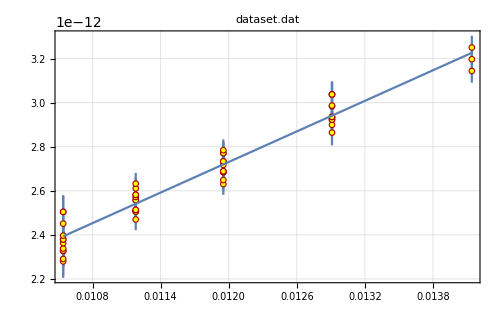
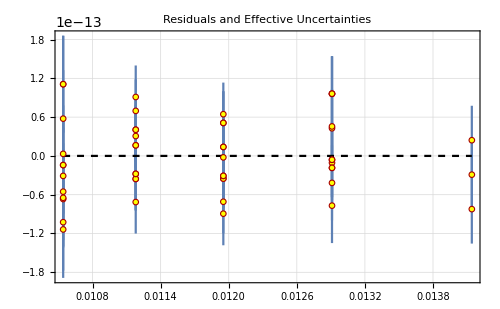
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-4.3699×10^-14 | b= 
2.31217×10^-10 | 
σ_a= 
9.56118×10^-14 | σ_b= 
8.02025×10^-12 | χ^2/(n-2)= 
1.0021

```mathematica
LinearDifferencePlot[]
```

We define a new function for calculating h in this case:

```mathematica
h2[slope_,error_]:={ScientificForm[(slope*Sqrt[2*mc2])/(x*c),3],ScientificForm[(error*Sqrt[2*mc2])/(x*c),2]}
```

```mathematica
h2all=h2[2.31217*10^-10,8.02025*10^-12]
```

{4.38×10^-15,1.5×10^-16}

Note that we had to remove the second and third graphite diffraction features from the dataset to get a reasonable collapse of the data points by our scaling (K̂)/(2π a_0). This indicates a large systematic error in those measurements. All calculated values for h are in eVs.

## Conclusion

```mathematica
summary=Join[{{"Feature","h (eVs)","σ_h (eVs)"}},{Join[{"First (Graphite)"},hg1]},{Join[{"Second (Graphite)"},hg2]},{Join[{"Third (Graphite)"},hg3]},{Join[{"First (Aluminium)"},ha1]},{Join[{"Second (Aluminium)"},ha2]},{Join[{"Third (Aluminium)"},ha3]},{Join[{"Overall"},h2all]}];
Grid[summary,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Feature | h (eVs) | σ_h (eVs)
First (Graphite) | 3.86×10^-15 | 1.7×10^-16
Second (Graphite) | 4.29×10^-15 | 1.1×10^-16
Third (Graphite) | 6.66×10^-15 | 7.9×10^-17
First (Aluminium) | 4.26×10^-15 | 2.5×10^-16
Second (Aluminium) | 5.09×10^-15 | 1.8×10^-16
Third (Aluminium) | 4.73×10^-15 | 1.5×10^-16
Overall | 4.38×10^-15 | 1.5×10^-16

For comparison, the NIST accepted value for h is 4.136×10^-15 eV.

We observe a large scattering of our estimates for h for each feature despite a good (around 1) (χ̃)^2 for each individual data set. This is due to two main issues with our data: few reliable data points and a large systematic error for each feature. One data set in particular seem to show significant systematic errors: the third graphite diffraction pattern. This is consistent with what we have found above - the measurements for the third feature of diffraction in graphite is not collapsed onto a collinear set with the rest of the data points by a scaling (K̂)/(2π a_0)as we would expect. This either indicates a large systematic error in our measurements for this feature, or that the small-angle approximation starts to fail for the third feature of graphite and onwards.

While the second diffraction pattern provides a reasonable estimate of h, we observe that its dataset is not collapsed by the scaling either. This dataset was discarded on the basis of internal inconsistencies (we had to remove a data point to obtain a linear fit, and even then the fit was significantly worse than most of the other data sets).

We collapsed the remaining data sets using the scaling and used a linear fit to obtain an estimate of h. We obtain h=(4.38±0.15)×10^-15 eVs, which is within two standard errors of the NIST value. This is a reasonable estimate with a very good (χ̃)^2 for the fit, indicating that our collapsed dataset is reasonably free of significant systematic errors (i.e. the systematic errors for each data point were probably independent and random to within the accuracy of the experiment).